```mathematica
Needs["HierarchicalClustering`"]
Hex2RGB=RGBColor@@(IntegerDigits[#~StringDrop~1~FromDigits~16,256,3]/255.)&;
colors={
{{"white","#fffefc"},{"pearl","#fbfcf7"},{"alabaster","#fefaf0"},{"snow","#f4fefd"},{"ivory","#fef7e5"},{"cream","#fffbda"},{"eggshell","#fef9e3"},{"cotton","#fbfcf7"},{"chiffon","#fafaf1"},{"salt","#f8efec"},{"lace","#faf3ea"},{"coconut","#fff1e6"},{"linen","#f2ebd3"},{"bone","#e7dfcc"},{"porcelain","#fffffc"},{"parchment","#fcf6df"},{"rice","#fbf6ef"}},{{"blue","#0074d9"},{"navy","#001f3f"},{"aqua","#7fdbff"},{"sky","#00b2ff"},{"teal","#39cccc"},{"slate","#757b87"},{"indigo","#281e5d"},{"cobalt","#1438bd"},{"ocean","#026063"},{"peacock","#002d37"},{"azure","#1621a6"},{"cerulean","#0592c2"},{"lapis","#2632c2"},{"spruce","#2c3e4b"},{"stone","#59788d"},{"aegean","#1e456e"},{"berry","#24146f"},{"denim","#141e3c"},{"admiral","#060f94"},{"sapphire","#52b2c0"},{"arctic","#82edfe"}},
{{"tan","#e5dbac"},{"beige","#ecdc99"},{"macaroon","#f7df75"},{"hazelwood","#c9bc8e"},{"granola","#d6b75a"},{"oat","#dec98a"},{"eggnog","#fbe29d"},{"fawn","#c7a951"},{"sand","#d7b963"},{"sepia","#e3b678"},{"latte","#e9c17b"},{"oyster","#dcd69f"},{"biscotti","#e3c565"},{"parmesean","#fee993"},{"hazelnut","#bda55d"},{"sandcastle","#dbc27d"},{"buttermilk","#fdefb2"},{"sanddollar","#ebe7b9"},{"shortbread","#fce791"}},
{{"yellow","#FFDC00"},{"canary","#fac801"},{"gold","#f9a602"},{"daffodil","#feee88"},{"flaxen","#d5b65a"},{"butter","#fee226"},{"lemon","#effd5f"},{"mustard","#e9b829"},{"corn","#e4cd04"},{"medallion","#e4b103"},{"dandelion","#fdce2a"},{"bumblebee","#fce206"},{"banana","#fcf4a3"},{"butterscotch","#fabd04"},{"dijon","#c29200"},{"honey","#ec9707"},{"blonde","#fdeb75"},{"pineapple","#ffe327"},{"tuscansun","#fcd12a"}},
{{"orange","#ff851b"},{"tangerine","#f98228"},{"merigold","#fdae1d"},{"cider","#b66827"},{"rust","#8c4005"},{"ginger","#bc5703"},{"tiger","#fb6b02"},{"bronze","#b2560c"},{"cantaloupe","#fca172"},{"apricot","#ed810f"},{"carrot","#ed7116"},{"squash","#c95c09"},{"spice","#7a3a03"},{"marmalade","#d16102"},{"amber","#893201"},{"sandstone","#d57128"},{"yam","#cc5801"}},{{"red","#ff4136"},{"cherry","#9a0f02"},{"rose","#e2252a"},{"jam","#600f0b"},{"merlot","#541f1b"},{"garnet","#5f0a04"},{"crimson","#b8100a"},{"ruby","#900503"},{"scarlet","#910d08"},{"redwine","#4c0805"},{"redapple","#a91b0d"},{"mahogany","#420d09"},{"blood","#710c04"},{"sangria","#5f1914"},{"currant","#670c07"},{"blush","#bb544a"},{"candy","#d31603"},{"lipstick","#9b0f02"}},{{"pink","#f69acd"},{"fuchsia","#f012be"},{"punch","#f25278"},{"watermelon","#fe809c"},{"flamingo","#fda4b8"},{"rouge","#f26c8c"},{"salmon","#fdab9f"},{"coral","#fe7d67"},{"peach","#fb9483"},{"strawberry","#fc4c4e"},{"rosewood","#a04242"},{"lemonade","#fabacb"},{"taffy","#fa85c4"},{"bubblegum","#fd5ca8"},{"balletslipper","#f69abf"},{"crepe","#f1b7c6"},{"maroon","#85144be"},{"hotpink","#ff1696"}},{{"purple","#b10dc9"},{"mauve","#7a4a89"},{"violet","#710193"},{"boysenberry","#630536"},{"lavender","#e3a0f6"},{"maroon","#85144B"},{"plum","#601a36"},{"lilac","#b65fcd"},{"periwinkle","#be93d4"},{"eggplant","#311431"},{"iris","#9866c5"},{"heather","#9b7cb9"},{"amethyst","#a45de4"},{"raisin","#290916"},{"orchid","#af69ee"},{"mulberry","#4d0220"}},{{"green","#2ecc40"},{"chartreuse","#b0fc37"},{"juniper","#395311"},{"sage","#728c69"},{"lime","#01ff70"},{"fern","#5dbc64"},{"olive","#98bf64"},{"emerald","#038911"},{"pear","#74b62d"},{"moss","#476d1e"},{"shamrock","#03ac13"},{"seafoam","#3cec96"},{"pine","#24501e"},{"parakeet","#02c04a"},{"mint","#98ecc3"},{"seaweed","#354b21"},{"pickle","#5a7d36"},{"pistachio","#b2d3c1"},{"basil","#32622d"},{"crocodile","#5f7c3a"}},
{{"brown","#241709"},{"coffee","#4b371c"},{"mocha","#3c290d"},{"peanut","#795c34"},{"carob","#35260f"},{"hickory","#371d10"},{"pecan","#4a2512"},{"walnut","#432711"},{"caramel","#66360f"},{"gingerbread","#5d2c04"},{"chocolate","#2c1603"},{"tortilla","#9a7b4f"},{"umber","#352415"},{"tawny","#7e491d"},{"brunette","#391e07"},{"cinammon","#642b0d"},{"penny","#522915"}},{{"grey","#aaaaaa"},{"shadow","#373737"},{"graphite","#584d5b"},{"iron","#332d31"},{"pewter","#6a6880"},{"cloud","#c5c5d0"},{"silver","#dddddd"},{"smoke","#59515f"},{"anchor","#42424c"},{"ash","#554c4d"},{"porpoise","#4d4c5d"},{"dove","#7c6e7f"},{"fog","#655965"},{"flint","#7d7c9c"},{"pebble","#333333"},{"lead","#403f4e"},{"coin","#9897a9"},{"fossil","#787276"}},{{"black","#111111"},{"ebony","#080401"},{"crow","#3d3934"},{"charcoal","#222023"}}};
```

```mathematica
crayons={{{"Mahogany","#CD4A4A"},{"Fuzzy Wuzzy Brown","#CC6666"},{"Chestnut","#BC5D58"},{"Red Orange","#FF5349"},{"Sunset Orange","#FD5E53"},{"Bittersweet","#FD7C6E"},{"Melon","#FDBCB4"},{"Outrageous Orange","#FF6E4A"},{"Vivid Tangerine","#FFA089"},{"Burnt Sienna","#EA7E5D"},{"Brown","#B4674D"},{"Sepia","#A5694F"},{"Orange","#FF7538"},{"Burnt Orange","#FF7F49"},{"Copper","#DD9475"},{"Mango Tango","#FF8243"},{"Atomic Tangerine","#FFA474"},{"Beaver","#9F8170"},{"Antique Brass","#CD9575"},{"Desert Sand","#EFCDB8"},{"Raw Sienna","#D68A59"},{"Tumbleweed","#DEAA88"},{"Tan","#FAA76C"},{"Peach","#FFCFAB"},{"Macaroni and Cheese","#FFBD88"},{"Apricot","#FDD9B5"},{"Neon Carrot","#FFA343"},{"Almond","#EFDBC5"},{"Yellow Orange","#FFB653"},{"Gold","#E7C697"},{"Shadow","#8A795D"},{"Banana Mania","#FAE7B5"},{"Sunglow","#FFCF48"},{"Goldenrod","#FCD975"},{"Dandelion","#FDDB6D"},{"Yellow","#FCE883"},{"Green Yellow","#F0E891"},{"Spring Green","#ECEABE"},{"Olive Green","#BAB86C"},{"Laser Lemon","#FDFC74"},{"Unmellow Yellow","#FDFC74"},{"Canary","#FFFF99"},{"Yellow Green","#C5E384"},{"Inch Worm","#B2EC5D"},{"Asparagus","#87A96B"},{"Granny Smith Apple","#A8E4A0"},{"Electric Lime","#1DF914"},{"Screamin Green","#76FF7A"},{"Fern","#71BC78"},{"Forest Green","#6DAE81"},{"Sea Green","#9FE2BF"},{"Green","#1CAC78"},{"Mountain Meadow","#30BA8F"},{"Shamrock","#45CEA2"},{"Jungle Green","#3BB08F"},{"Caribbean Green","#1CD3A2"},{"Tropical Rain Forest","#17806D"},{"Pine Green","#158078"},{"Robin Egg Blue","#1FCECB"},{"Aquamarine","#78DBE2"},{"Turquoise Blue","#77DDE7"},{"Sky Blue","#80DAEB"},{"Outer Space","#414A4C"},{"Blue Green","#199EBD"},{"Pacific Blue","#1CA9C9"},{"Cerulean","#1DACD6"},{"Cornflower","#9ACEEB"},{"Midnight Blue","#1A4876"},{"Navy Blue","#1974D2"},{"Denim","#2B6CC4"},{"Blue","#1F75FE"},{"Periwinkle","#C5D0E6"},{"Cadet Blue","#B0B7C6"},{"Indigo","#5D76CB"},{"Wild Blue Yonder","#A2ADD0"},{"Manatee","#979AAA"},{"Blue Bell","#ADADD6"},{"Blue Violet","#7366BD"},{"Purple Heart","#7442C8"},{"Royal Purple","#7851A9"},{"Purple Mountain Majesty","#9D81BA"},{"Violet {Purple}","#926EAE"},{"Wisteria","#CDA4DE"},{"Vivid Violet","#8F509D"},{"Fuchsia","#C364C5"},{"Shocking Pink","#FB7EFD"},{"Pink Flamingo","#FC74FD"},{"Plum","#8E4585"},{"Hot Magenta","#FF1DCE"},{"Purple Pizzazz","#FF1DCE"},{"Razzle Dazzle Rose","#FF48D0"},{"Orchid","#E6A8D7"},{"Red Violet","#C0448F"},{"Eggplant","#6E5160"},{"Cerise","#DD4492"},{"Wild Strawberry","#FF43A4"},{"Magenta","#F664AF"},{"Lavender","#FCB4D5"},{"Cotton Candy","#FFBCD9"},{"Violet Red","#F75394"},{"Carnation Pink","#FFAACC"},{"Razzmatazz","#E3256B"},{"Piggy Pink","#FDD7E4"},{"Jazzberry Jam","#CA3767"},{"Blush","#DE5D83"},{"Tickle Me Pink","#FC89AC"},{"Pink Sherbet","#F780A1"},{"Maroon","#C8385A"},{"Red","#EE204D"},{"Radical Red","#FF496C"},{"Mauvelous","#EF98AA"},{"Wild Watermelon","#FC6C85"},{"Scarlet","#FC2847"},{"Salmon","#FF9BAA"},{"Brick Red","#CB4154"},{"White","#EDEDED"},{"Timberwolf","#DBD7D2"},{"Silver","#CDC5C2"},{"Gray","#95918C"},{"Black","#232323"}}};
```

## Exploration of the Space

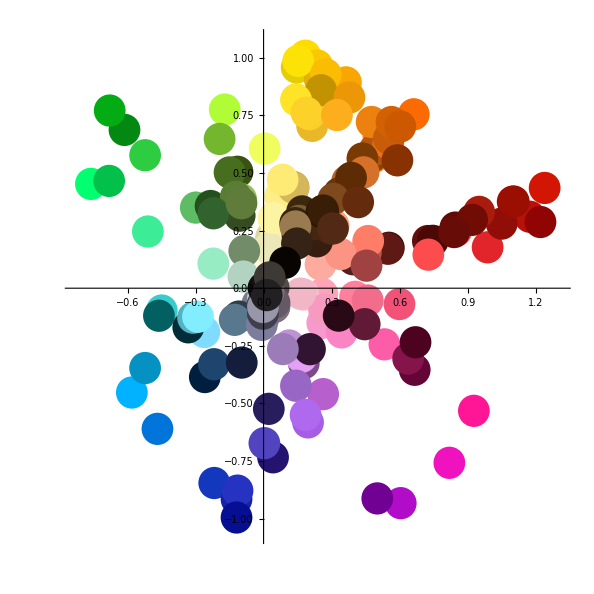

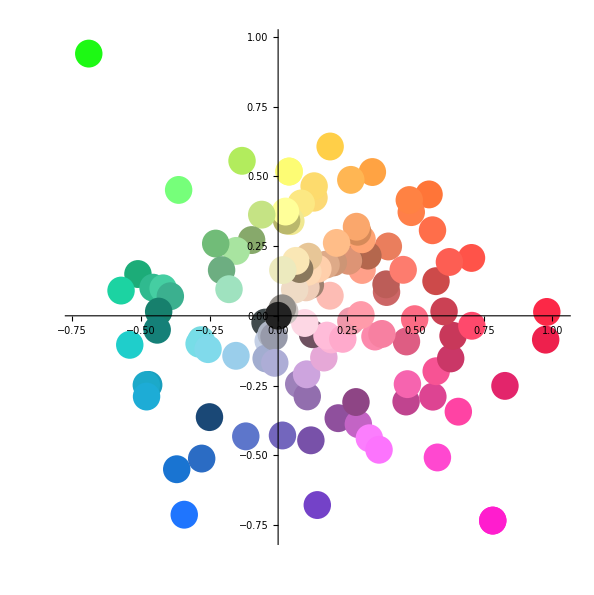

```mathematica
Show@@{(MapAt[Graphics[{#, Disk[ColorConvert[#,"LUV"][[{2,3}]],0.07]}]&@Hex2RGB[#]&,#,2]&/@#&/@colors)[[;;,;;,2]],Axes->True,AxesOrigin->{0,0} }
Show@@{(MapAt[Graphics[{#, Disk[ColorConvert[#,"LUV"][[{2,3}]],0.05]}]&@Hex2RGB[#]&,#,2]&/@#&/@crayons)[[;;,;;,2]],Axes->True,AxesOrigin->{0,0} }
```

## Color Distance

```mathematica
Clear[DL,Sl,kl,DCab,kc,Sc,DHab,kh,Sh,C1,C2,cone,ctwo,e]
cdist94[{l1_,a1_,b1_},{l2_,a2_,b2_}]:=Evaluate@Function[{l1,a1,b1,l2,a2,b2},
Evaluate[#1//.#2&[Sqrt[(DL/kl/Sl)^2+(DCab /kc/Sc)^2+(DHab/kh/Sh)^2],
{DL->l1-l2,
DHab->Sqrt[(a1-a2)^2+(b1-b2)^2-DCab^2],
DCab->C1-C2,
C1->Sqrt[a1^2+b1^2],
C2->Sqrt[a2^2+b2^2],
Sl->1,
Sc->1+K1 C1,
Sh->1+K2 C1,
kl->1,
K1->0.045,
K2->0.015,
kc->1,
kh->1}]]
][l1,a1,b1,l2,a2,b2]

Clear[DLp, Lbar, Cbar, a1p, a2p, Cbarp, C1p,C2p,h1p,h2p,cdist00,ciede2000]
cdist00[{l1_,a1_,b1_},{l2_,a2_,b2_}]:=ciede2000[100{l1,a1,b1},100{l2,a2,b2}];
ciede2000[{l1_,a1_,b1_},{l2_,a2_,b2_}]:=
Module[{DLp,Lbar, C1,C2,Cbar,G,a1p, a2p, C1p,C2p,Cbarp,DCp,h1p,h2p,dhp,DHp,hbarp,T,Sl,Sc,Sh,Rt,kc=1,kh=1,kl=1,e00},
DLp=l2-l1;
Lbar=(l1+l2)/2;
C1=Sqrt[a1^2+b1^2];
C2=Sqrt[a2^2+b2^2];
Cbar=(C1+C2)/2;
G=1/2(1-Sqrt[Cbar^7/(Cbar^7+25^7)]);
a1p=a1 (1+G);
a2p=a2 (1+G);
C1p=Chop@Sqrt[a1p^2+b1^2];
C2p=Chop@Sqrt[a2p^2+b2^2];
Cbarp=(C1p+C2p)/2;
DCp=C2p-C1p;
h1p=Mod[ArcTan[a1p,b1],2Pi]/Degree;
h2p=Mod[ArcTan[a2p,b2],2Pi]/Degree;
hbarp=Mod[ArcTan[a1p+a2p,b1+b2],2Pi]/Degree;
dhp=Mod[(h2p-h1p+180),360]-180;
DHp=2Sqrt[C1p C2p]Sin[dhp Degree/2];
T=1-0.17Cos[Degree(hbarp-30)]+0.24Cos[Degree(2 hbarp)]+0.32Cos[Degree(3hbarp+6)]-0.2Cos[Degree(4hbarp-63)];
Sl=1+(0.015(Lbar-50)^2)/Sqrt[20+(Lbar-50)^2];Sc=1+0.045Cbarp;Sh=1+0.015Cbarp T;
Rt=-2Sqrt[Cbarp^7/(Cbarp^7+25^7)]Sin[Degree(60Exp[-((hbarp-275)/25)^2])];
kc=1;kh=1;kl=1;
e00=Sqrt[(DLp/kl/Sl)^2+(DCp/kc/Sc)^2+(DHp/kh/Sh)^2+Rt(DCp/kc/Sc)(DHp/kh/Sh)];
Return[e00];
]
```

## Clustering and Grouping

```mathematica
kruskal[pts_]:=Module[{n=Length[pts[[2]]],vpairs,jj=0,hh,pair,dist,c1,c2,c1c2},Do[hh[k]={k},{k,n}];
vpairs=Sort[Flatten[Table[{pts[[k,l]],{k,l}},{k,1,n-1},{l,k+1,n}],1]];
First[Last[Reap[While[jj<Length[vpairs],jj++;
{dist,pair}=vpairs[[jj]];
{c1,c2}={hh[pair[[1]]],hh[pair[[2]]]};
If[c1=!=c2,Sow[vpairs[[jj,2]]];
c1c2=Union[c1,c2];
Do[hh[c1c2[[k]]]=c1c2,{k,Length[c1c2]}];
If[Length[hh[pair[[1]]]]==n,Break[]];];]]]]];
```

```mathematica
With[{mat=#1,edges=kruskal@#1},System`Graph[
#[[1]]<->#[[2]]&/@ edges,
ImagePadding->10,GraphLayout->"SpringElectricalEmbedding",
System`VertexStyle->MapIndexed[#2[[1]]->Directive[Hex2RGB@#1]&,Flatten[colors,1][[;;,2]] ],
VertexSize->3,
System`EdgeWeight-> (Part@@Flatten[{{mat},#},1]&/@edges)
]]&[DistanceMatrix[#,DistanceFunction->cdist00]&@Flatten[(MapAt[ColorConvert[#,"LAB"]&@Hex2RGB[#]&,#,2]&/@#&/@colors),1][[;;,2]] ]
```

```mathematica
SizeSplit[size_]:=Flatten[#,1]&@CondClusterSplit[#,#[[4]]+#[[5]]>size&]&
CondClusterSplit[clist_,cond_]:=Map[If[And[Head@#===Cluster,cond@#],ClusterSplit[#,2],{#}]&,clist];
GeneralClusterFlatten[c_]:=If[Head@c===Cluster,ClusterFlatten@c,{c}];
(GeneralClusterFlatten/@SizeSplit[8]@SizeSplit[10]@SizeSplit[10]@SizeSplit[10]@#&@(ClusterSplit[#,15]&@Agglomerate[Flatten[(MapAt[ColorConvert[#,"LAB"]&@Hex2RGB[#]&,#,2]&/@#&/@#),1][[;;,2]]->Range[Length@Flatten[#,1]] ,Linkage->"Ward",DistanceFunction->cdist00])/.Dispatch@MapIndexed[#2[[1]]->Graphics[{Hex2RGB@#1[[2]],Disk[]},ImageSize->22]&,Flatten[#,1]]//Map[TableForm,#]& )&@colors
```

{-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-}

```mathematica
Map[Graphics[{RGBColor@ColorConvert[#,"LAB"->"RGB"],Disk[]},ImageSize->30]&,#]&/@
(GeneralClusterFlatten/@
Flatten[CondClusterSplit[#,#[[4]]+#[[5]]>7&],1]&@
(ClusterSplit[#,20]&@
Agglomerate[
(ColorConvert[1-#&/@Hex2RGB@#[[2]],"LAB"]&/@Flatten[colors[[{3,4,5,6,7,8,10}]],1 ])
 ,Linkage->"Ward" ,DistanceFunction->cdist00])) //Map[TableForm,SortBy[#,Length]]&
```

{-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-}

```mathematica
BorderedOuter[f_,l1_,l2_]:=BorderedOuter[f,Identity,l1,l2]
BorderedOuter[f_,d_,l1_,l2_]:=Transpose[{Prepend[d/@l1,""]}~Join~Transpose[{d/@l2}~Join~Outer[f,l1,l2,1]]]
Graphics[{RGBColor@ColorConvert[#,"LAB"->"RGB"],Disk[]},ImageSize->30]&
```

```mathematica
MinDistElems[d_,l1_,l2_]:=Transpose[{d/@l1}~Join~Transpose[{d@Part[l2,Ordering[#1,1][[1]] ],Min@#1}&/@Outer[,l1,l2,1]]]//SortBy[#,-#[[3]]&]&

NMostDifferent[d_,initial_,n_]:=Module[{i,next={},closest=initial},
For[i=1,i≤n,i++,
AppendTo[next,{"","#"<>StringJoin[IntegerString[#,16,2]&@Round@#&/@(255*ColorConvert[#[[1,1]],"LAB"->"RGB"])]}&@closest];
closest = Map[With[{distance=d@@{#[[1]],closest[[1,1]]}},If[distance < #[[3]],{#[[1]],closest[[1,1]],distance},#]]&,closest[[2;;]]]//SortBy[#,-#[[3]]&]&;
];
Return[{next,closest}];
]
```

```mathematica
diffs=MinDistElems[Identity,
(*Graphics[{RGBColor@ColorConvert[#,"LUV"->"RGB"],Disk[]},ImageSize->100]&,*)
(ColorConvert[1-#&/@Hex2RGB@#[[2]],"LAB"]&/@Flatten[colors[[{3,4,5,6,7,8,10}]],1 ]),
ColorConvert[#,"LAB"]&/@Hex2RGB/@Flatten[colors[[;;,;;,2]],1]
];
```

```mathematica
MapAt[Graphics[{RGBColor@ColorConvert[#,"LAB"->"RGB"],Disk[]},ImageSize->30]&,#,{{1},{2}}]&/@diffs
```

{{-Graphics-,-Graphics-,11.8762},{-Graphics-,-Graphics-,11.6001},{-Graphics-,-Graphics-,11.0505},{-Graphics-,-Graphics-,10.8085},{-Graphics-,-Graphics-,10.667},{-Graphics-,-Graphics-,10.1456},{-Graphics-,-Graphics-,9.89382},{-Graphics-,-Graphics-,9.89347},{-Graphics-,-Graphics-,9.80292},{-Graphics-,-Graphics-,9.65301},{-Graphics-,-Graphics-,9.57127},{-Graphics-,-Graphics-,9.56404},{-Graphics-,-Graphics-,9.46526},{-Graphics-,-Graphics-,9.23838},{-Graphics-,-Graphics-,9.21183},{-Graphics-,-Graphics-,9.01953},{-Graphics-,-Graphics-,8.72498},{-Graphics-,-Graphics-,8.70322},{-Graphics-,-Graphics-,8.6151},{-Graphics-,-Graphics-,8.59291},{-Graphics-,-Graphics-,8.59175},{-Graphics-,-Graphics-,8.57667},{-Graphics-,-Graphics-,8.38209},{-Graphics-,-Graphics-,8.34793},{-Graphics-,-Graphics-,8.13192},{-Graphics-,-Graphics-,8.05314},{-Graphics-,-Graphics-,8.04991},{-Graphics-,-Graphics-,7.94254},{-Graphics-,-Graphics-,7.71122},{-Graphics-,-Graphics-,7.65505},{-Graphics-,-Graphics-,7.57397},{-Graphics-,-Graphics-,7.36577},{-Graphics-,-Graphics-,7.33038},{-Graphics-,-Graphics-,7.19818},{-Graphics-,-Graphics-,7.14262},{-Graphics-,-Graphics-,7.04496},{-Graphics-,-Graphics-,7.02835},{-Graphics-,-Graphics-,6.9866},{-Graphics-,-Graphics-,6.83328},{-Graphics-,-Graphics-,6.74783},{-Graphics-,-Graphics-,6.72706},{-Graphics-,-Graphics-,6.5744},{-Graphics-,-Graphics-,6.43401},{-Graphics-,-Graphics-,6.42669},{-Graphics-,-Graphics-,6.39431},{-Graphics-,-Graphics-,6.38418},{-Graphics-,-Graphics-,6.35529},{-Graphics-,-Graphics-,6.15926},{-Graphics-,-Graphics-,6.12481},{-Graphics-,-Graphics-,6.10207},{-Graphics-,-Graphics-,6.09999},{-Graphics-,-Graphics-,6.0927},{-Graphics-,-Graphics-,6.06455},{-Graphics-,-Graphics-,6.04384},{-Graphics-,-Graphics-,6.04218},{-Graphics-,-Graphics-,6.02198},{-Graphics-,-Graphics-,6.00925},{-Graphics-,-Graphics-,5.80194},{-Graphics-,-Graphics-,5.77414},{-Graphics-,-Graphics-,5.71025},{-Graphics-,-Graphics-,5.67547},{-Graphics-,-Graphics-,5.65168},{-Graphics-,-Graphics-,5.63776},{-Graphics-,-Graphics-,5.61734},{-Graphics-,-Graphics-,5.61544},{-Graphics-,-Graphics-,5.56238},{-Graphics-,-Graphics-,5.38274},{-Graphics-,-Graphics-,5.31283},{-Graphics-,-Graphics-,5.28546},{-Graphics-,-Graphics-,5.27613},{-Graphics-,-Graphics-,5.21497},{-Graphics-,-Graphics-,5.19539},{-Graphics-,-Graphics-,5.11022},{-Graphics-,-Graphics-,4.90636},{-Graphics-,-Graphics-,4.89941},{-Graphics-,-Graphics-,4.89764},{-Graphics-,-Graphics-,4.85775},{-Graphics-,-Graphics-,4.85586},{-Graphics-,-Graphics-,4.84976},{-Graphics-,-Graphics-,4.78524},{-Graphics-,-Graphics-,4.66695},{-Graphics-,-Graphics-,4.64807},{-Graphics-,-Graphics-,4.61696},{-Graphics-,-Graphics-,4.58789},{-Graphics-,-Graphics-,4.58207},{-Graphics-,-Graphics-,4.51784},{-Graphics-,-Graphics-,4.51244},{-Graphics-,-Graphics-,4.41398},{-Graphics-,-Graphics-,4.38687},{-Graphics-,-Graphics-,4.33603},{-Graphics-,-Graphics-,4.26457},{-Graphics-,-Graphics-,4.2506},{-Graphics-,-Graphics-,4.17418},{-Graphics-,-Graphics-,4.15335},{-Graphics-,-Graphics-,4.12956},{-Graphics-,-Graphics-,4.06671},{-Graphics-,-Graphics-,4.03396},{-Graphics-,-Graphics-,3.96499},{-Graphics-,-Graphics-,3.90394},{-Graphics-,-Graphics-,3.89637},{-Graphics-,-Graphics-,3.84867},{-Graphics-,-Graphics-,3.80148},{-Graphics-,-Graphics-,3.78483},{-Graphics-,-Graphics-,3.76937},{-Graphics-,-Graphics-,3.75217},{-Graphics-,-Graphics-,3.67889},{-Graphics-,-Graphics-,3.66645},{-Graphics-,-Graphics-,3.43686},{-Graphics-,-Graphics-,3.38269},{-Graphics-,-Graphics-,3.36146},{-Graphics-,-Graphics-,3.29914},{-Graphics-,-Graphics-,3.25042},{-Graphics-,-Graphics-,3.21539},{-Graphics-,-Graphics-,2.86889},{-Graphics-,-Graphics-,2.78958},{-Graphics-,-Graphics-,2.75586},{-Graphics-,-Graphics-,2.53632},{-Graphics-,-Graphics-,2.36512},{-Graphics-,-Graphics-,2.3021},{-Graphics-,-Graphics-,2.2008},{-Graphics-,-Graphics-,2.12967},{-Graphics-,-Graphics-,1.75321},{-Graphics-,-Graphics-,1.69769},{-Graphics-,-Graphics-,1.14178}}

```mathematica
Graphics[{Hex2RGB[#],Disk[]},ImageSize->70]&/@NMostDifferent[cdist00,diffs,30][[1,;;,2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics[{#,Disk[]},ImageSize->40]&/@(Hex2RGB/@Flatten[#,1]&@colors[[2,;;,2]]//SortBy[#,#[[3]]&] &)
Graphics[{#,Disk[]},ImageSize->40]&/@(Hex2RGB/@Flatten[#,1]&@colors[[9,;;,2]]//SortBy[#,#[[2]]&] &)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}